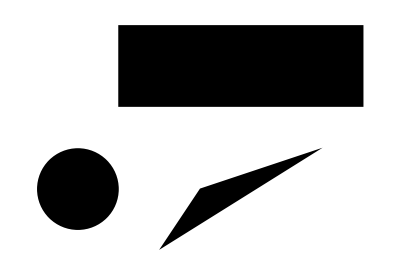

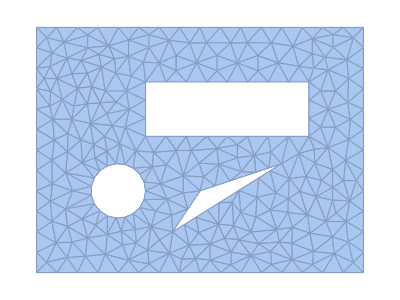

502

-Graphics-

75

```mathematica
Geometry={Disk[],Rectangle[{1,2},{7,4}],Triangle[{{3,0},{6,1},{2,-1.5}}]};

Graphics[Geometry]

DiscretizeRegion[RegionDifference[Rectangle[{-3,-3},{9,6}],RegionUnion@@Geometry]]
MeshCellCount[%,2]

HighlightMesh[bMesh=BoundaryMesh[DiscretizeRegion[RegionUnion@@Geometry]],Labeled[0,"Index"]]
NEl=MeshCellCount[%,1]
```

```mathematica
GreenF[x_,x0_]:=-N[1/2/Pi Log[Norm[x-x0]]]
DGreenF[x_,x0_]:=-N[1/2/Pi/Norm[x-x0]]

BElts=MeshPrimitives[bMesh,1];
Knots=RegionCentroid/@BElts;
```

```mathematica
Lab=RegionMeasure/@BElts;
```

```mathematica
G=Table[Lab[[i]]×NIntegrate[GreenF[BElts[[i,1,1]]+t×(BElts[[i,1,2]]-BElts[[i,1,1]]),Knots[[j]]],{t,0,1}]
,{j,1,NEl},{i,1,NEl}];
```

```mathematica
a=Table[(BElts[[i,1,2]]-BElts[[i,1,1]])/Norm[BElts[[i,1,2]]-BElts[[i,1,1]]],{i,1,NEl}];
n=Transpose[{-a[[All,2]],a[[All,1]]}];
H=Table[Lab[[i]]×NIntegrate[DGreenF[BElts[[i,1,1]]+t×(BElts[[i,1,2]]-BElts[[i,1,1]]),Knots[[j]]]((BElts[[i,1,1]]+t×(BElts[[i,1,2]]-BElts[[i,1,1]])-Knots[[j]])/Norm[(BElts[[i,1,1]]+t×(BElts[[i,1,2]]-BElts[[i,1,1]])-Knots[[j]])]).n[[i]]
,{t,0,1}]
,{j,1,NEl},{i,1,NEl}];
```

```mathematica
u0 = Table[Piecewise[{{1,i<35},{2,34<i<60}},3],{i,1,NEl}] ;
```

```mathematica
q0 =Chop[ LinearSolve[G,(1/2IdentityMatrix[NEl]+H).u0]];
```

```mathematica
q0
```

{-1.79282,-0.934929,-0.742042,-0.645491,-0.621774,-0.641398,-0.689395,-0.758164,-0.828199,-0.846778,-0.963035,-2.42084,-1.35159,-0.845585,-0.72421,-0.710466,-0.804495,-1.2377,-2.159,-0.737566,-0.521974,-0.460894,-0.430488,-0.417536,-0.415731,-0.423645,-0.443923,-0.486215,-0.558631,-1.01945,-1.25374,-0.874295,-0.960718,-1.81661,-0.101248,-0.0458067,0.522972,1.51772,0.947919,0.804645,0.686558,0.59766,0.500646,0.358761,0.165322,0.153931,-0.103069,-0.345213,-0.533891,-1.12293,-1.23213,-0.467265,-0.380488,-0.324513,-0.281933,-0.253542,-0.227491,-0.194852,-0.161181,1.07931,1.25067,1.44259,1.63075,1.72181,1.63565,1.3807,1.04019,0.709583,0.442458,0.235601,0.0737138,-0.0452071,-0.123677,-0.166894,-0.179328,-0.161677,-0.111319,-0.0234435,0.108066,0.287135,0.501868,0.717433,0.908412}

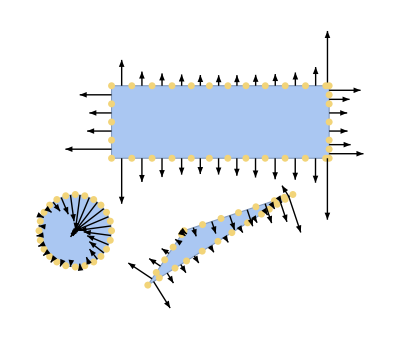

```mathematica
Show[HighlightMesh[bMesh,0],Graphics[{Arrowheads[.02],Table[Arrow[{Knots[[i]],Knots[[i]]-0.7(q0[[i]]{#[[2]],-#[[1]]}/Norm[#]&[(BElts[[i,1,2]]-BElts[[i,1,1]])])}],{i,1,NEl}]}]]
```